# Solar Magnetohydrodynamics: Applications.

## Chapter 1: exercise 1

## Pressure

```mathematica
(*Parameters*)
rho=5*10^-13;         (*Density in kg/m^3*)
R=8.314;              (*Ideal gas constant in J/(mol K)*)
muTilde=0.6;          (*Mean molecular weight*)

(*Pressure calculation*)
p[T_]:=rho*R*T/muTilde

(*Evaluation for T=10^6 K*)
pVal=p[10^6]
```

6.92833×10^-6

## Thermal conductivity timescale

```mathematica
(*Additional Parameters*)gamma=5/3;
kappaParallel[T_]:=10^-11 T^(5/2);  (*Thermal conductivity*)
LValues={10^6,10^7,10^8};         (*Characteristic length scales in meters*)

(*Thermal conduction time scale*)
tauCond[T_,L_]:=(gamma*p[T]*L^2)/((gamma-1)*kappaParallel[T]*T)

(*Plot for different characteristic lengths*)
Plot[Evaluate[Table[tauCond[T,L],{L,LValues}]],{T,10^4,10^7},PlotRange->{10^-5,10^7},PlotLabels->(StringJoin["L = ",ToString[#/10^6]," Mm"]&/@LValues),AxesLabel->{"T (K)","τ_cond (s)"},ScalingFunctions->{"Log","Log"},(*Logarithmic scale on both axes*)PlotStyle->{Red,Blue,Green},GridLines->Automatic]
```

-Graphics-

## Radiation timescale

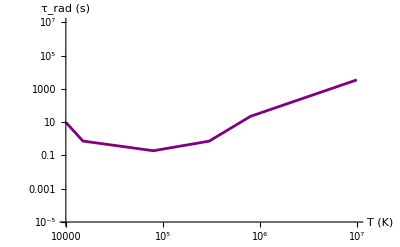

```mathematica
(*Parameters for the piecewise cooling function*)chiValues={{1.76*10^-13,7.4},(*T≤1.5×10^4 K*){4.29*10^10,1.8},(*1.5×10^4<T≤8×10^4 K*){2.86*10^19,0.0},(*8×10^4<T≤3×10^5 K*){1.41*10^33,-2.5},(*3×10^5<T≤8×10^5 K*){1.97*10^24,-1.0}       (*T>8×10^5 K*)};

(*Function to obtain chi*and alpha as a function of T*)
getChiAlpha[T_]:=Which[T<=1.5*10^4,{1.76*10^-13,7.4},T<=8*10^4,{4.29*10^10,1.8},T<=3*10^5,{2.86*10^19,0.0},T<=8*10^5,{1.41*10^33,-2.5},T>8*10^5,{1.97*10^24,-1.0}];

(*Radiation time scale*)
tauRad[T_]:=Module[{chi,alpha},{chi,alpha}=getChiAlpha[T];
(gamma*p[T])/((gamma-1)*rho^2*chi*T^alpha)];

(*Plot of τ_rad*)
Plot[tauRad[T],{T,10^4,10^7},PlotRange->{10^-5,10^7},AxesLabel->{"T (K)","τ_rad (s)"},ScalingFunctions->{"Log","Log"},PlotStyle->{Purple},GridLines->Automatic]
```

## Comparison between τ_cond y τ_rad

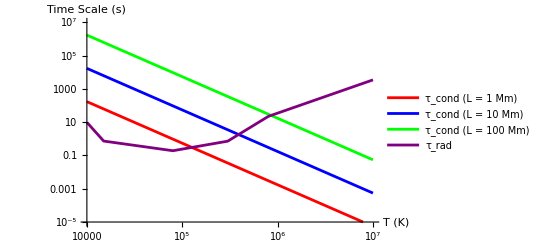

```mathematica
(*Comparison Plot*)
Plot[{tauCond[T,10^6],tauCond[T,10^7],tauCond[T,10^8],tauRad[T]},{T,10^4,10^7},PlotRange->{10^-5,10^7},AxesLabel->{"T (K)","Time Scale (s)"},ScalingFunctions->{"Log","Log"},(*Logarithmic scale on both axes*)PlotStyle->{Red,Blue,Green,Purple},(*Colors for each curve*)PlotLegends->{"τ_cond (L = 1 Mm)","τ_cond (L = 10 Mm)","τ_cond (L = 100 Mm)","τ_rad"},GridLines->Automatic]
```